```mathematica
(*Subscript[f, column]*)
Nn= 4;
Manipulate[Grid@Table[Subscript[c, n] e^(i n Subscript[x, k]),{n,0,nmax},{k,0,kmax}],{nmax,0,Nn-1},{kmax,0,Nn-1}]
```

```mathematica
(*Subscript[c, row]*)
Manipulate[Grid@Join[
Table[Subscript[f, k] e^(-i n Subscript[x, k]),{n,0,nmax},{k,0,kmax}],
Table[{0,1,4,9}[[k+1]]Exp[-(ⅈ 2π n k)/4],{n,0,nmax},{k,0,kmax}]
],{nmax,0,Nn-1},{kmax,0,Nn-1}]
(*Manipulate[Grid@Table[{0,1,4,9}[[k+1]]Exp[-(ⅈ 2π n k)/4],{n,0,nmax},{k,0,kmax}],{nmax,0,3},{kmax,0,3}]*)
```

```mathematica
dft[f_List]:= With[{t=Length[f]},Table[Total@Table[f[[k+1]]Exp[-(ⅈ 2π n k)/t],{k,0,t-1}],{n,0,t-1}]]
dft[{0,1,4,9}]
```

{14,-4+8 ⅈ,-6,-4-8 ⅈ}

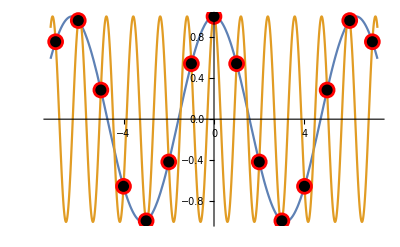

```mathematica
points1 = Join[{PointSize[0.03]},Table[{Red,Point[{i,Cos[i]}]},{i,-7,7}]];
points2 = Join[{PointSize[0.02]},Table[{Black,Point[{i,Cos[(2π-1)i]}]},{i,-7,7}]];
Plot[{Cos[t],Cos[(2π-1)t]},{t,-2.3π,2.3π},Epilog->Join[points1,points2]]
```

```mathematica
2Fourier[{0,1,4,9}]
```

{14.+0. ⅈ,-4.-8. ⅈ,-6.+0. ⅈ,-4.+8. ⅈ}

```mathematica
fft[{x_,y_},n_] := x+y Exp[-ⅈ π n ]
fft[f_List,n_]:=fft[Downsample[f,2,1],n]+Exp[-(ⅈ 2π n)/Length[f]]fft[Downsample[f,2,2],n]
fft[f_List]:= Table[fft[f,n]//N,{n,0,Length[f]-1}]
Column@fft[{0,1,4,9}]
fft[{1,0},0]
fft[{4,9},0]
```

14.
-4.+8. ⅈ
-6.
-4.-8. ⅈ

1

13

{{-102.4,1.×10^6},{-102.3,1.×10^6},{-102.2,1.×10^6},{-102.1,1.×10^6},{-102.,1.×10^6},{-101.9,1.×10^6},{-101.8,1.×10^6},{-101.7,1.×10^6},{-101.6,1.×10^6},{-101.5,1.×10^6}}

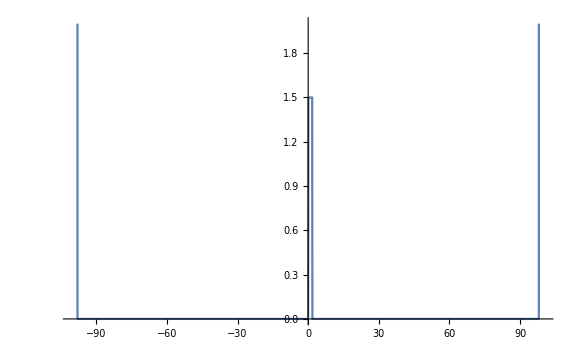

```mathematica
Take[dataV, 10]
(*ListLinePlot[dataV, PlotRange->{{-100,100},{0,2}}, ImageSize->Large]*)
```

```mathematica
Take[dataC, 10]
(*Manipulate[ListLinePlot[Take[dataC, {2*i-1,2*i}],PlotRange->{{-100,100},{0,2}}], {i, 1,Length@dataC/2, 1}]*)
```

{{-34.4474,0.},{-34.4474,1.},{-34.2537,0.},{-34.2537,1.},{-34.0601,0.},{-34.0601,1.},{-33.8664,0.},{-33.8664,1.},{-33.6728,0.},{-33.6728,1.}}

Take::normal: Nonatomic expression expected at position 1 in Take[dataC,{1,2}].

ListLinePlot::lpn: Take[dataC,{1,2}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Take::normal: Nonatomic expression expected at position 1 in Take[dataC,{1,2}].

ListLinePlot::lpn: Take[dataC,{1,2}] is not a list of numbers or pairs of numbers.

Take::normal: Nonatomic expression expected at position 1 in Take[dataC,{1,2}].

ListLinePlot::lpn: Take[dataC,{1,2}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Take::normal: Nonatomic expression expected at position 1 in Take[dataC,{1,2}].

ListLinePlot::lpn: Take[dataC,{1,2}] is not a list of numbers or pairs of numbers.

```mathematica
Take[dataX, 10]
nt = Length@dataC/2;
nx = Length@dataX/nt
(*Manipulate[ListLinePlot[Take[dataX, {nx*i+1,nx*(i+1)}],PlotRange->{{-100,100},{0,2}}, ImageSize->Large], {i, 0,nt-1, 1}]*)
```

{{-102.4,0.},{-102.3,0.},{-102.2,0.},{-102.1,0.},{-102.,0.},{-101.9,0.},{-101.8,0.},{-101.7,0.},{-101.6,0.},{-101.5,0.}}

2048

Take::normal: Nonatomic expression expected at position 1 in Take[dataX,{1+381 nx,382 nx}].

ListLinePlot::lpn: Take[dataX,{1+381 nx,382 nx}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{{-102.4,0.},{-102.3,0.},{-102.2,0.},{-102.1,0.},{-102.,0.},{-101.9,0.},{-101.8,0.},{-101.7,0.},{-101.6,0.},{-101.5,0.},{-101.4,0.},{-101.3,0.},{-101.2,0.},{-101.1,0.},{-101.,0.},«22»,{-98.7,0.},{-98.6,0.},{-98.5,0.},{-98.4,0.},{-98.3,0.},{-98.2,0.},{-98.1,0.},{-98.,0.},{-97.9,0.},{-97.8,0.},{-97.7,0.},{-97.6,0.},{-97.5,0.},«942030»},«1»].

$Aborted[]

ListLinePlot::lpn: Take[{{-102.4,0.},{-102.3,0.},{-102.2,0.},{-102.1,0.},{-102.,0.},{-101.9,0.},{-101.8,0.},{-101.7,0.},{-101.6,0.},{-101.5,0.},{-101.4,0.},{-101.3,0.},{-101.2,0.},{-101.1,0.},{-101.,0.},«22»,{-98.7,0.},{-98.6,0.},{-98.5,0.},{-98.4,0.},{-98.3,0.},{-98.2,0.},{-98.1,0.},{-98.,0.},{-97.9,0.},{-97.8,0.},{-97.7,0.},{-97.6,0.},{-97.5,0.},«942030»},«1»] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
Take[dataK, 10]
nt = Length@dataC/2;
nk = Length@dataK/nt
(*Manipulate[ListLinePlot[Take[dataK, {nk*i+1,nk*(i+1)}],PlotRange->{{-10,10},{0,3}}, ImageSize->Large], {i, 0,nt-1, 1}]*)
```

{{-28.,0.},{-27.9693,0.},{-27.9386,0.},{-27.908,0.},{-27.8773,0.},{-27.8466,0.},{-27.8159,0.},{-27.7852,0.},{-27.7546,0.},{-27.7239,0.}}

2048

Take::normal: Nonatomic expression expected at position 1 in Take[dataK,{1+206 nk,207 nk}].

ListLinePlot::lpn: Take[dataK,{1+206 nk,207 nk}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{{-28.,0.},{-27.9693,0.},{-27.9386,0.},{-27.908,0.},{-27.8773,0.},{-27.8466,0.},{-27.8159,0.},{-27.7852,0.},{-27.7546,0.},{-27.7239,0.},{-27.6932,0.},{-27.6625,0.},«27»,{-26.8035,0.},{-26.7728,0.},{-26.7421,0.},{-26.7115,0.},{-26.6808,0.},{-26.6501,0.},{-26.6194,0.},{-26.5887,0.},{-26.5581,0.},{-26.5274,0.},{-26.4967,0.},«942030»},{1+206 nk,207 nk}].

ListLinePlot::lpn: Take[{{-28.,0.},{-27.9693,0.},{-27.9386,0.},{-27.908,0.},{-27.8773,0.},{-27.8466,0.},{-27.8159,0.},{-27.7852,0.},{-27.7546,0.},{-27.7239,0.},{-27.6932,0.},{-27.6625,0.},«27»,{-26.8035,0.},{-26.7728,0.},{-26.7421,0.},{-26.7115,0.},{-26.6808,0.},{-26.6501,0.},{-26.6194,0.},{-26.5887,0.},{-26.5581,0.},{-26.5274,0.},{-26.4967,0.},«942030»},{1+206 nk,207 nk}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

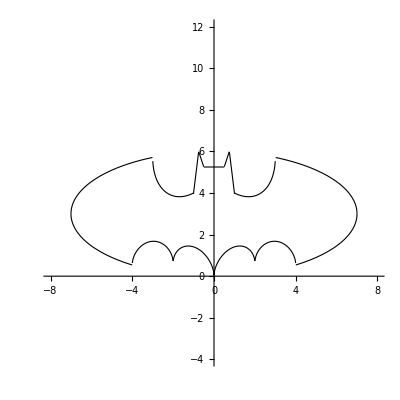

```mathematica
f1 [x_]:= 3 √(-(x/7)^2+1)
f2[x_]:=-f1[x]
f3 [x_]:= Abs@(x/2)-(3 √33-7)/112 x^2+√(1-(Abs[Abs@x-2]-1)^2)-3
f4[x_]:=9-8Abs@x
f5[x_]:=3Abs@x+.75
f6[x_]:=2.25
f7[x_]:=1.5-.5Abs@x-(6 √10)/14(√(3-x^2+2Abs@x)-2)
Plot[
{
Piecewise[{
{3+f1[x],Abs@x≥3.01}, 
{3+f4[x], 0.75≤ Abs@x≤ 1.01},
{3+f5[x], .5≤ Abs@x≤ .75},
{3+f6[x], Abs@x≤ .5},
{3+f7[x],Abs@x≥ 1}}],
Piecewise[{
{3+f2[x],Abs@x≥ 4},
{3+f3[x],Abs@x≤ 4}}]
},
{x,-7,7},
PlotRange->{{-8,8},{-4,12}},
PlotStyle->{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},
AspectRatio->Full]
battop[x_]:=Piecewise[{
{3+f1[x],Abs@x≥3.01}, 
{3+f4[x], 0.75≤ Abs@x≤ 1.01},
{3+f5[x], .5≤ Abs@x≤ .75},
{3+f6[x], Abs@x≤ .5},
{3+f7[x],Abs@x≥ 1}}]
```

```mathematica
path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho1/QuantumPython/";dataX = Import[path <> "QuantumPythonX.txt", "Data"];
dataK = Import[path <> "QuantumPythonK.txt", "Data"];
dataV = Import[path <> "QuantumPythonV.txt", "Data"];
dataC = Import[path <> "QuantumPythonC.txt", "Data"];
```

```mathematica
nt = Length@dataC/2;
n = Length@dataK/nt;
m = 1.;
V0 = 1.5;
p0=Sqrt[2m 0.5V0];
sqrt2mV0= Sqrt[2m V0];
battoppts=Table[{i,battop@i},{i,Range[-7,7,0.01]}];
plotX[t_] := ListLinePlot[
{
Take[dataX, {n*(t-1)+1,n*t}],
dataV,
Take[dataC, {2*t-1,2*t}],
battoppts
},
PlotStyle->
{
{Red},
{Black,Thickness[0.002]},
{Black,Dotted},
{Black,Thickness[0.002]}
},
PlotRange->{{-30,30},{0,15/2}}, 
ImageSize->Large,
PerformanceGoal->"Quality",
PlotLegends->{"|ψ(x)|","V(x)","x_0+v_0t"},
AxesLabel->{"x","|ψ(x)|"},
AxesOrigin->{-30,0},
PlotRangePadding->{{0.1,0.2},{0.01,0}},
AspectRatio->1/8]
plotK[t_] := ListLinePlot[
{
Take[dataK, {n*(t-1)+1,n*t}],
{{-p0,0},{-p0,3}},
{{p0,0},{p0,3}},
{{sqrt2mV0,0},{sqrt2mV0,3}}
},
PlotStyle->
{
{Red},
{Black,Dotted},
{Black,Dashed},
{Black,Dotted}
},
PlotRange->{{-4,4},{0,2.5}}, 
ImageSize->Large,
PerformanceGoal->"Quality",
PlotLegends->{"|ψ^─(k)|","±p0","√(2 SubscriptBox[mV, 0])"},
AxesLabel->{"x","|ψ^─(k)|"},
AxesOrigin->{-4,0},
PlotRangePadding->{0,0.01},
AspectRatio->1/8]
```

```mathematica
(*plotsX = Table[plotX[t],{t, 1,nt, 1}];
plotsK = Table[plotK[t],{t, 1,nt, 1}];*)
```

```mathematica
Manipulate[Column@{plotX[t],plotK[t]},{t, 1,nt,1, AnimationRate->4}](*Manipulate[Column@{plotsX[[Round[100*t]]],plotsK[[Round[100*t]]]},{t, 0.01,nt/100, 0.01, AnimationRate->10}]*)
(*Manipulate[Column@{plotsX[[Round[100*t]]],plotsK[[Round[100*t]]]},{t, 0.01,nt/100, 0.01, AnimationRate-> 20}]*)
(*Manipulate[Round[10*t],{t, 0.1,10*nt, 0.1}]*)
```

```mathematica
nt
```

460

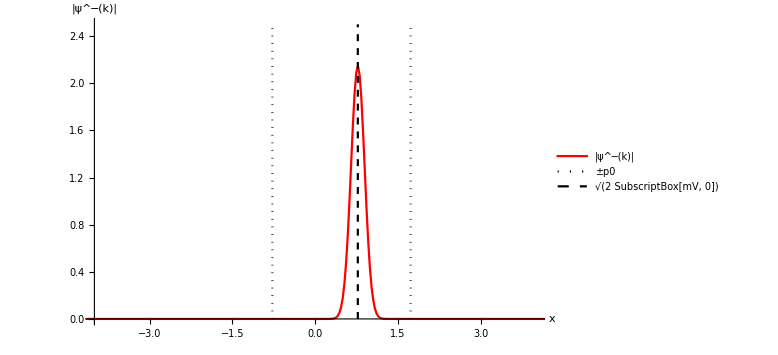

```mathematica
ListLinePlot[
{
Take[dataK, {nx*(1-1)+1,nx*1}],
{{-p0,0},{-p0,3}},
{{p0,0},{p0,3}},
{{sqrt2mV0,0},{sqrt2mV0,3}}
},
PlotStyle->
{
{Red},
{Black,Dotted},
{Black,Dashed},
{Black,Dotted}
},
PlotRange->{{-4,4},{0,2.5}}, 
ImageSize->Large,
PerformanceGoal->"Quality",
PlotLegends->{"|ψ^─(k)|","±p0","√(2 SubscriptBox[mV, 0])"},
AxesLabel->{"x","|ψ^─(k)|"},
AxesOrigin->{-4,0},
PlotRangePadding->{0,0.01}]
```

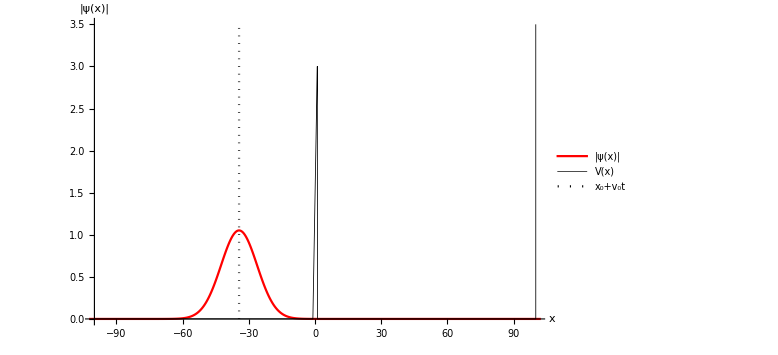

```mathematica
ListLinePlot[
{
Take[dataX, {nx*(1-1)+1,nx*1}],
dataV,
Take[dataC, {2*1-1,2*1}]
},
PlotStyle->
{
{Red},
{Black,Thickness[0.002]},
{Black,Dotted}
},
PlotRange->{{-100,100},{0,3.5}}, 
ImageSize->Large,
PerformanceGoal->"Quality",
PlotLegends->{"|ψ(x)|","V(x)","x_0+v_0t",""},
AxesLabel->{"x","|ψ(x)|"},
AxesOrigin->{-100,0},
PlotRangePadding->{{0.1,0.2},{0.01,0}}
]
```

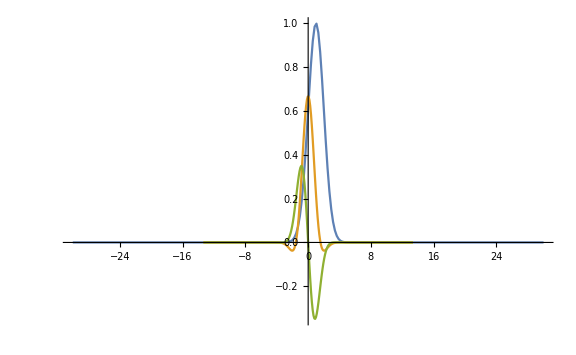

```mathematica
dft[ts_List,fs_List]:= (
l=Length[ts]; 
dt=Abs@ts[[2]]-Abs@ts[[1]]//Abs;
w0 = -π/dt;
ws=Array[#&,l,{-Abs@w0,Abs@w0}];
dw=Abs@ws[[2]]-Abs@ws[[1]]//Abs;
t0=ts[[1]] ;
gs=Table[Total@Table[fs[[k+1]]Exp[-ⅈ (w0+n*dw)(t0+k*dt)],{k,0,l-1}],{n,0,l-1}]/Sqrt[l-1];
(*gs = Exp[-ⅈ*Outer[Times,ws,ts]].fs/Sqrt[l-1];*)
grpts = Riffle[ws//N,Re@gs//N]~Partition~2;
gipts = Riffle[ws//N,Im@gs//N]~Partition~2;
fpts = Riffle[ts//N,fs//N]~Partition~2;
{fpts,grpts,gipts}
(*ListLinePlot[{fpts,gpts},PlotRange->Full,ImageSize->Large]*)
)
gaussian[t_, m_, s_]:=Exp[-(t-m)^2/(2 s^2)];
t0 = -30;
l=2^8;
ts=Array[#&,l,{-Abs@t0,Abs@t0}];
gdatasimple = dft[ts,Table[gaussian[t, 1, 1],{t,ts}]];
ListLinePlot[gdatasimple,PlotRange->Full, ImageSize->Large]
```

```mathematica
gdata= Table[dft[ts,Table[gaussian[t, m, s],{t,ts}]],{m,-1,1,1},{s,0.5,2,0.5}];
```

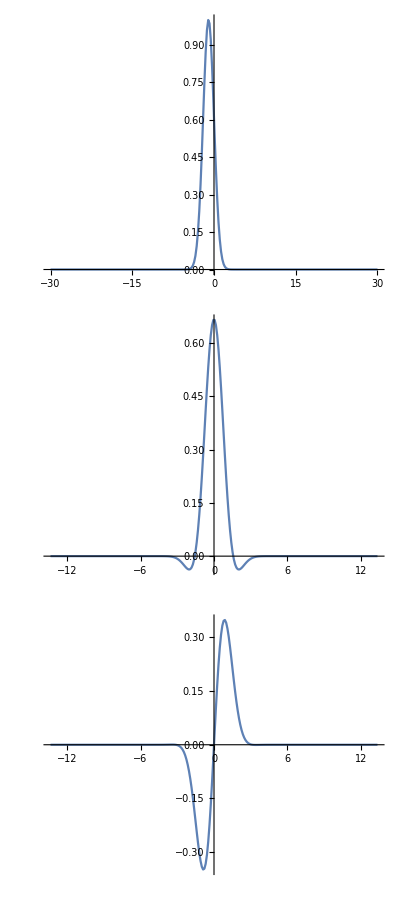

```mathematica
Column@Table[ListLinePlot[gdata[[1]][[2]][[i]],PlotRange->Full, ImageSize->Medium],{i,1,3,1}]
```

```mathematica
Manipulate[ListLinePlot[gdata[[m+2]][[Round[2*s]]],PlotRange->Full,ImageSize->Large],{m,-1,1,1},{s,0.5,2,0.5}]
```

Part::partd: Part specification gdata⟦3⟧ is longer than depth of object.

ListLinePlot::lpn: gdata is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
osc[t_]:=Sin[10t]Exp[-t];
l=2^8;
ts=Array[#&,l,{0,10}];
odata=dft[ts,osc/@ts];
```

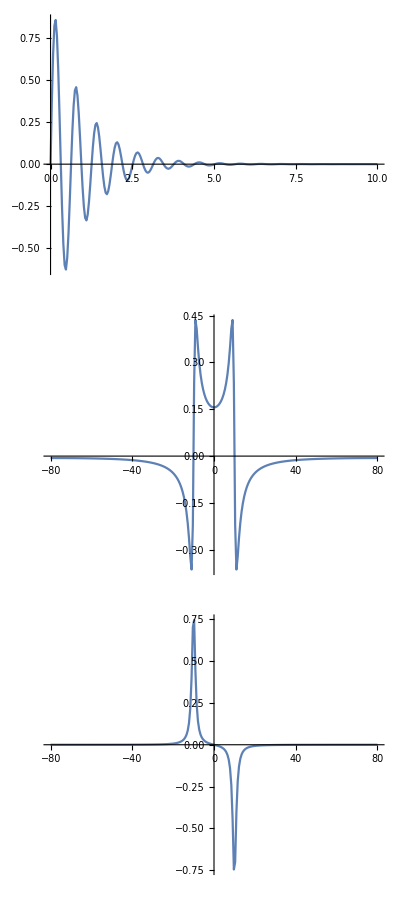

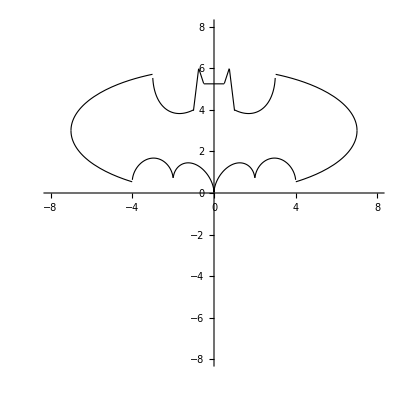

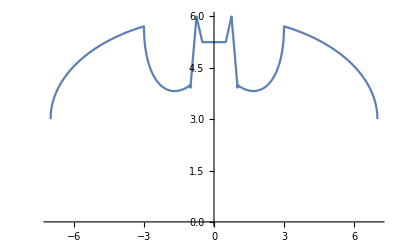

```mathematica
Column@Table[ListLinePlot[odata[[i]],PlotRange->Full, ImageSize->Medium],{i,1,3,1}]
```